```mathematica
eqn1 = (Lnw + Ls1)y1  - Ls1 y2 - (i1 -inw -iloop)Rs1 + inw Rnw == 0
```

inw Rnw-(i1-iloop-inw) Rs1+(Lnw+Ls1) y1-Ls1 y2==0

```mathematica
eqn1
```

inw Rnw-(i1-iloop-inw) Rs1+(Lnw+Ls1) y1-Ls1 y2==0

```mathematica
eqn2 = Lnw y1 + inw Rnw == iloop RT + LT y2
```

inw Rnw+Lnw y1==iloop RT+LT y2

```mathematica
Solve[{eqn1 ,eqn2},{y1,y2}]//FullSimplify
```

{{y1→(-inw Ls1 Rnw-i1 LT Rs1+iloop LT Rs1+inw LT (Rnw+Rs1)+iloop Ls1 RT)/(Lnw Ls1-(Lnw+Ls1) LT),y2→((-i1+iloop) Lnw Rs1+inw (-Ls1 Rnw+Lnw Rs1)+iloop (Lnw+Ls1) RT)/(Lnw Ls1-(Lnw+Ls1) LT)}}

```mathematica
Pulse shape
```

```mathematica
Landau
```

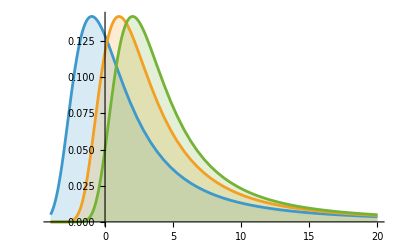

```mathematica
Plot[Table[PDF[LandauDistribution[μ,2],x],{μ,{-1,1,2}}]//Evaluate,{x,-4,20},Filling->Axis]
```

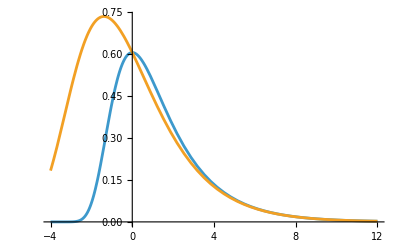

```mathematica
Plot[{Exp[(- (x+Exp[-x]))/2],Exp[(- ((x)+Exp[-x*0.5]))/2]},{x, -4, 12}]
```

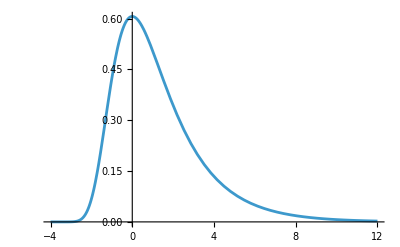

```mathematica
Plot[{Exp[(- (x+Exp[-x]))/2]},{x, -4, 12}]
```

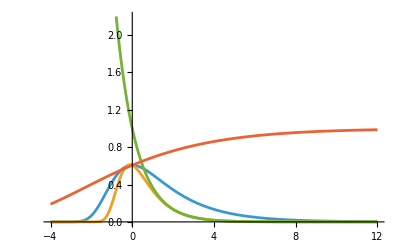

```mathematica
Plot[{Exp[(- (x+Exp[-x]))/2],Exp[(- (x*2+Exp[-x/0.6]))/2],Exp[(- (x*2))/2],Exp[(- Exp[-x*0.3])/2]},{x, -4, 12}]
```

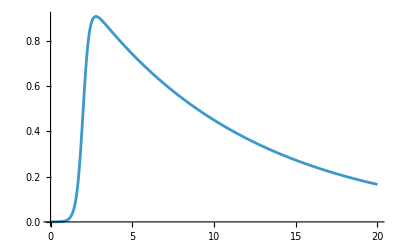

```mathematica
Plot[(1- 1/(Exp[(x-2)/0.2]+1))*Exp[- ((x-2)*0.1)],{x,0,20}]
```